```mathematica
(**Definition of some physical constants**)
m=1.67*10^(-27);(*neutron-mass in kg*)
hbar=1.054*10^(-34);
atomicu=1.67*10^(-27);
eV=1.602*10^(-19);
konstant0=2*m/hbar^2*eV/1000; (*konstant corresponds to 2m/hbar^2 and possesses units 1/m^2/meV*)
```

```mathematica
(**Incident neutron beam directed along the axis {0,1,0} of the laboratory coordinate system**)
Ei=12;(*indicent neutron energy in meV*)
lambdafromEnergy[En_]:=2*Pi/Sqrt[konstant0]/Sqrt[En];
lambdai:=lambdafromEnergy[Ei];(*wave-length of incident neutrons in 10^(-10) m*)
ki:={0,1,0}*2*Pi/lambdai;(*wave-vector of incident neutrons*)
(**Characterization of the sample, here we work with a cubic sample. But the procedure can easily be adjusted for lower crystal-symmetries**)
(*Note: All length-scales are given in m, except for the sample-dimensions, which are given in mm*)
a=4.689*10^(-10);(*Lattice parameter of the cubic sample*)
d0=0.7;(*Thickness of the plate-like samples*)
rhoIn=5.546;(*Density of Indium in CeIn3, given in units g/cm^3*)
mIn=114.818;(*Atomic mass of Indium in units u*)
sigmaIn=193.8;(*Neutron absorption cross section of Indiumin units barn, cf. Ref. V.F.Sears,Neutron News 3,26 (1992).*)
muIn0=rhoIn*sigmaIn/(mIn*atomicu)*10^(-27);
muIn=1.77;(*Absorption-Coefficient due to indium in CeIn3 in 1/cm*)
```

```mathematica
(**Definition of reciprocal space vectors and scattering angles**)
Q[{h_,k_,l_}]:=2*Pi/a*{h,k,l};
Qnorm[{h_,k_,l_}]:=2*Pi/a*Sqrt[h^2+k^2+l^2];
AngleAlpha[h_,k_,l_,En_]:=ArcCos[-(konstant0*En+(Qnorm[{h,k,l}])^2)/(2*Sqrt[konstant0]*Sqrt[Ei]*Qnorm[{h,k,l}])];(*Alpha corresponds to the angle between incident neutrons*)
(*and a given energy-transfer En*)
Theta[{h_,k_,l_}]:=ArcSin[lambdai/2*Sqrt[(h^2+k^2+l^2)/a^2 ]];
```

```mathematica
(**Transmission and absorption for neutrons*)

(*Note: the absorption cross-section due to indium corresponds to neutrons of wavelength 1.798A. We assume a linear wave-length dependence.*)

Absorption[L_,En_]:=1-Exp[-lambdafromEnergy[En]/(1.798*10^(-10))/(1/muIn0*10)*L];(*Here En corresponds to the energy of neutrons and L to the traveled path length.*)
Transmission[L_,En_]:=Exp[-lambdafromEnergy[En]/(1.798*10^(-10))/(1/muIn0*10)*L];
```

```mathematica
(**Here, we transform the sample-coordinate system into the lab coordinate-syste^m.**)
(*Unit-vectirs pointing along the three basis-vectors of the conventional cubic basis:*)
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};
Qphys[{h_,k_,l_}]:=Q[{h,k,l}].{1,1,0}/Sqrt[2]*e1+Q[{h,k,l}].{0,0,-1}*e2+Q[{h,k,l}].{1,-1,0}/Sqrt[2]*e3;(*The wave-vector {h,k,l} in the lab-frame of the unrotated sample. Note: The orientation-matrix was fixed on the spectrometer*)
R[angle_]:=RotationMatrix[angle,{0,0,1}];(*Azimuthal rotation performed during a Horace-scan*)
BraggAngle[h_,k_,l_,En_]:=x/.NSolve[VectorAngle[R[x].(Qphys[{h,k,l}]),ki]==AngleAlpha[h,k,l,En]&&(R[x].(Qphys[{h,k,l}])).{1,0,0}<0&&0<=x<2 Pi  ,x,Reals][[1]]//Chop(*This function calculates the angle at that the scattering condition is satisfied*)
Deff[RotationAngle_]:=Abs[d0/Cos[RotationAngle]];(*Effective path in the sample of neutrons that do not scatter.*)

SampleNormal[RotationAngle_]:=R[RotationAngle].{0,1,0};(*Direction of the direction that is normal to the sample-plate*)

Qphysrot[{h_,k_,l_,En_}]:=R[BraggAngle[h,k,l,En]].(Qphys[{h,k,l}]);(*Direction of the Q-vector in the lab-frame in the situation, where the scattering condition is fulfilled*)
kf[h_,k_,l_,En_]:=ki+R[BraggAngle[h,k,l,En]].(Qphys[{h,k,l}]);(*Final wave-vector, i.e., of neutrons that were scattered.*)
kf2[h_,k_,l_,En_,Braggangle_]:=ki+R[Braggangle].(Qphys[{h,k,l}]);
```

```mathematica
(**We now assume that neutrons enter the plate-like sample at one of its large surfaces. The neutrons 1) first travel a distance x1, 2) then they are scattered into the direction kf2, and 3) eventually they travel again through the sample unti they leyve the sample.**)

Pathlength2[h_,k_,l_,En_,x1_,BraggAngle_]:=Module[{h0=h,k0=k,l0=l,En0=En,x10=x1,BraggAngle0=BraggAngle,result,effectivesnormal},
effectivesnormal=SampleNormal[BraggAngle0]*Sign[SampleNormal[BraggAngle0].Normalize[ki]];
If[ effectivesnormal.kf2[h0,k0,l0,En0,BraggAngle0]>0,result=(d0-x10*Normalize[ki].effectivesnormal)/((Sign[effectivesnormal.kf2[h0,k0,l0,En0,BraggAngle0]]*Normalize[kf2[h0,k0,l0,En0,BraggAngle0]]).effectivesnormal)                    ];
If[ effectivesnormal.kf2[h0,k0,l0,En0,BraggAngle0]<0,result=(x10*Normalize[ki].effectivesnormal)/((Sign[effectivesnormal.kf2[h0,k0,l0,En0,BraggAngle0]]*Normalize[kf2[h0,k0,l0,En0,BraggAngle0]]).effectivesnormal)                    ];

Abs[result]
]
(*The last function calculates the pathlength of the neutrons within the sample after the scattering process*)
TransmissionTwoPathsb[{h_,k_,l_,En_,x1_,BraggAngle_}]:=Transmission[x1,Ei]*Transmission[Pathlength2[h,k,l,En,x1,BraggAngle],Ei-En];(*The last function calculates the total transmission of neutrons on the combined path before and after the scattering process*)
```

```mathematica
(**We now devided the sample into N tinier platelets of thickness d/N**)
```

```mathematica
ModuleTransmissionTotal[{h_,k_,l_,En_,N_}]:=Module[{h0=h,k0=k,l0=l,En0=En,N0=N,Braggangle,result,resultMatrix},
Braggangle=BraggAngle[h0,k0,l0,En0];

result=NSum[   TransmissionTwoPathsb[{h0,k0,l0,En0,(i-1)/N0*Deff[Braggangle],Braggangle}]   ,{i,1,N0}]*1/N0//Chop;
result
]
```

```mathematica
(*The last function gives an adequate description of the neutron absorption in a plate-like sample*)
```

```mathematica
(**Example: Absorption of neutrons scattering with wave-vector Q={-0.2,-0.2,0.2} and energy-transfer 1 meV. The sample is devided into 10 sublplatelets.**)
```

```mathematica
ModuleTransmissionTotal[{-0.2,-0.2,0.2,1,10}]
```

0.527465

```mathematica
(**With N=10, we get a relatively good approximation of the real abosrption coefficient already:**)
```

```mathematica
ConvergenceTest=Table[{i,ModuleTransmissionTotal[{-0.2,-0.2,0.2,1,i}]},{i,1,30}];
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

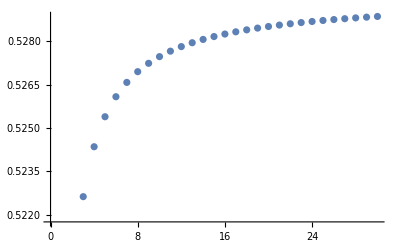

```mathematica
ListPlot[ConvergenceTest]
```